```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/hybrid_tail/math

```mathematica
M=10^-2;
ϕc=Sqrt[2]M;
```

## quadratic

```mathematica
Π2=100;
μ1=Π2/(M^2 ϕc)
Λ=(As 12 π^2 μ1^-2)^(1/4)/.{As->2.1 10^-9}
ψr=Sqrt[(Λ^4 Sqrt[Π2])/(48Sqrt[2 π^3])]
μ2=10.7;
```

50000000 √2

2.65572×10^-6

1.14716×10^-12

### N = 2

```mathematica
ys={y1,y2};
pys={py1,py2};
wys={wy1,wy2};
ny=Length[ys];
ysN=Table[ys[[i]][NN],{i,ny}];
pysN=Table[pys[[i]][NN],{i,ny}];
```

```mathematica
V[x_,ys_]:=Λ^4((1-(ys.ys)/M^2)^2+2(x^2 ys.ys)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2)
```

```mathematica
Vr[x_,yr_]=Λ^4((1-yr^2/M^2)^2+2(x^2 yr^2)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
ηr[x_,yr_]=D[D[Vr[x,yr], yr], yr]/Vr[x,yr];
```

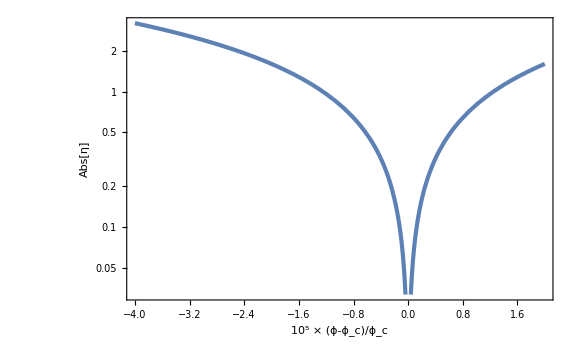

```mathematica
LogPlot[Abs[ηr[ϕc(1+dx 10^-5),0]],{dx,-4,2},GridLines->{None,{2}},FrameLabel->{Row[{"10^5 × ",(ϕ-Subscript[ϕ, "c"])/Subscript[ϕ, "c"]}],Abs[η]}]
```

```mathematica
H[x_,ys_,px_,pys_]:=Sqrt[(px^2/2+(pys.pys)/2+V[x,ys])/3]
```

```mathematica
EoMx={ⅆx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](px[NN]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwx[NN]),
ⅆpx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3px[NN]-D[V[x[NN],ysN], x[NN]]/H[x[NN],ysN,px[NN],pysN])ⅆNN};
EoMy=Flatten[Table[{ⅆysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](pysN[[i]]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwys[[i]][NN]),
ⅆpysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3pysN[[i]]-D[V[x[NN],ysN], ysN[[i]]]/H[x[NN],ysN,px[NN],pysN])ⅆNN},{i,ny}]];
```

```mathematica
IV=Flatten[{ϕc(*+15/μ1*),0,Table[ψr,{i,ny}],Table[0,{i,ny}],0}];
```

```mathematica
prob=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Flatten[{x[NN],px[NN],ysN,pysN,Ninf[NN]}],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
```

```mathematica
Nf=25;
sample=RandomFunction[prob,{0,Nf,0.01}];
```

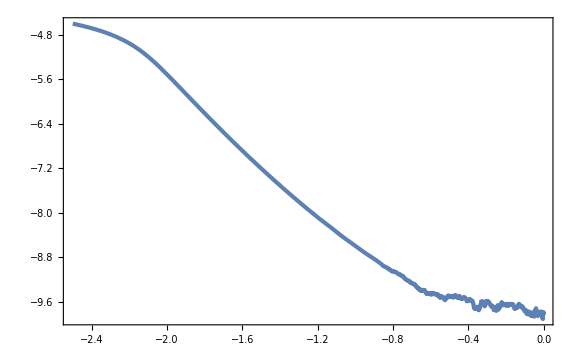

```mathematica
ParametricPlot[{(sample["PathFunction"][NN][[1]]-ϕc)/ϕc 10^5,Log10[Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]/M]},{NN,0,Nf}]
```

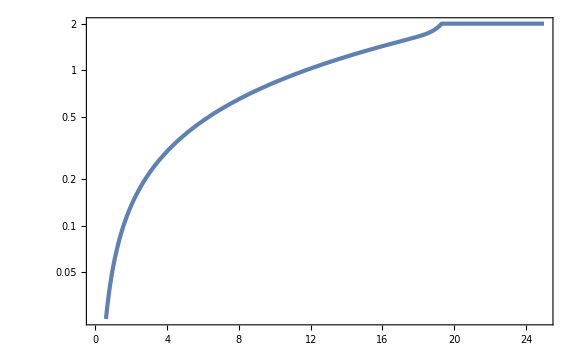

```mathematica
LogPlot[Abs[ηr[sample["PathFunction"][NN][[1]],Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]]],{NN,0,Nf}]//Quiet
```

```mathematica
deltaN=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Ninf[NN],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
Nf=25;
dNsampling=ParallelTable[RandomFunction[deltaN,{0,Nf,0.01}(*,10^3*)]["LastValues"],10^4]//Flatten;//AbsoluteTiming
```

{19.3526,Null}

```mathematica
Export["N=2_1e4.csv",dNsampling];
```

```mathematica
dNsamplingN2=Import["N=2_1e4.csv"]//Flatten;
```

```mathematica
Mean[dNsamplingN2]
Variance[dNsamplingN2-Mean[dNsamplingN2]]
```

19.0643

0.163953

```mathematica
Vx[x_]=Λ^4(1+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
Hx[x_,p_]=Sqrt[(p^2/2+Vx[x])/3];
ηrx[x_]=ηr[x,0];
```

```mathematica
Hxin=Hx[ϕc+15/μ1,0];
tf=50/Hxin;
hillsol=NDSolve[{x''[t]+3Hx[x[t],x'[t]]x'[t]+Vx'[x[t]]==0,NN'[t]==Hx[x[t],x'[t]],x[0]==ϕc+15/μ1,x'[0]==0,NN[0]==0,WhenEvent[ηrx[x[t]]==-2,Nend=NN[t];"StopIntegration"]},{x[t],NN[t]},{t,0,tf}][[1]];
```

```mathematica
Nend-Mean[dNsamplingN2]
```

2.0412

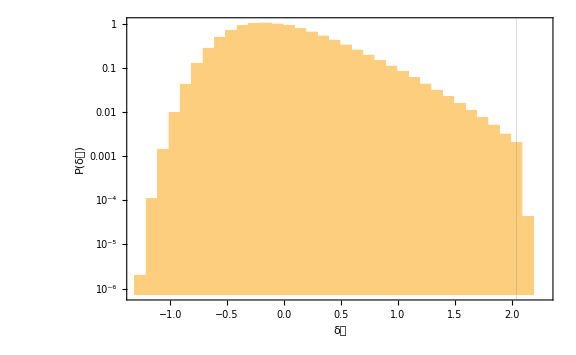

```mathematica
Histogram[dNsamplingN2-Mean[dNsamplingN2],{-131/100,231/100,1/10},{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,n==2}},PlotRange->Full,GridLines->{{Nend-Mean[dNsamplingN2]},None}]
```

```mathematica
dNpartN2=Partition[dNsamplingN2,10^6];
```

```mathematica
binListN2=HistogramList[dNsamplingN2-Mean[dNsamplingN2],{-131/100,221/100,1/10},"PDF"][[1]];
```

```mathematica
HistoListN2=Table[HistogramList[dNpartN2[[i]]-Mean[dNpartN2[[i]]],{binListN2},"PDF"][[2]],{i,Length[dNpartN2]}]//Transpose;
```

```mathematica
JackHistoN2=Table[{(binListN2[[i]]+binListN2[[i+1]])/2,Mean[HistoListN2[[i]]]±StandardDeviation[HistoListN2[[i]]]/Sqrt[10]},{i,Length[binListN2]-1}];
JackHistoWOEN2=Table[{(binListN2[[i]]+binListN2[[i+1]])/2,Mean[HistoListN2[[i]]]},{i,Length[binListN2]-1}];
JackHistoErrN2=Table[StandardDeviation[HistoListN2[[i]]]/Sqrt[10],{i,Length[binListN2]-1}];
```

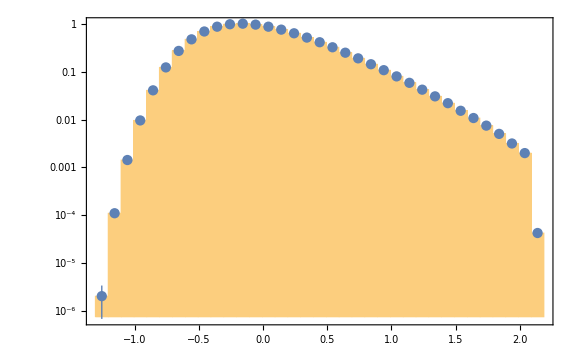

```mathematica
Show[Histogram[dNsamplingN2-Mean[dNsamplingN2],{binListN2},{"Log","PDF"},PlotRange->Full],ListLogPlot[JackHistoN2,Joined->False]]
```

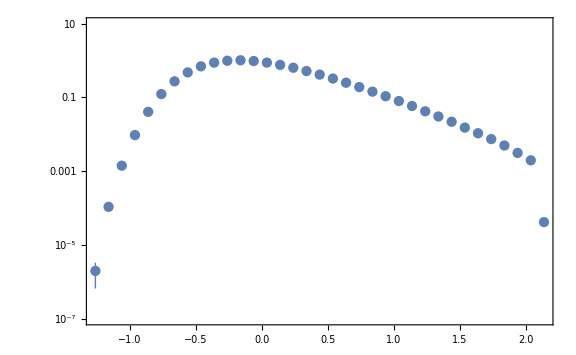

```mathematica
ListLogPlot[JackHistoN2,Joined->False,PlotRange->{10^-7,10}]
```

```mathematica
SUfitN2=NonlinearModelFit[JackHistoWOEN2,PDF[JohnsonDistribution["SU",γ,δ,μ,σ],x],{γ,δ,μ,σ},x(*,Weights->1/JackHistoErrN2^2*),MaxIterations->1000]
```

FittedModel[(1.20603 ⅇ^(-1/2 («1»)^2))/(√(0.272379+(«19»+x)^2))]

```mathematica
SUfitN2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
γ | -4.57126 | 0.209034 | -21.8685 | 2.11094×10^-20
δ | 3.02307 | 0.0382516 | 79.0312 | 2.5397×10^-37
μ | -1.18559 | 0.0250514 | -47.3264 | 1.78205×10^-30
σ | 0.521899 | 0.0181367 | 28.7759 | 6.29565×10^-24

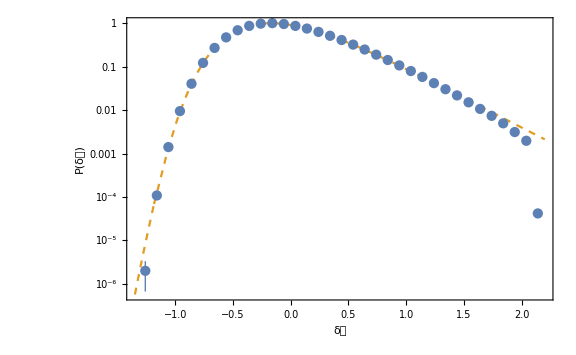

```mathematica
Show[LogPlot[Normal[SUfitN2],{x,-1.35,2.2},PlotStyle->{Color[2],Dashed},GridLines->{{Nend-Mean[dNsampling]},None},FrameLabel->{{P[δ𝒩],None},{δ𝒩,n==2}}],ListLogPlot[JackHistoN2,Joined->False]]
```

```mathematica
D[Log[Normal[SUfitN2]], x]/.{x->1}
```

-2.98353

### N = 15

```mathematica
ys={y1,y2,y3,y4,y5,y6,y7,y8,y9,y10,y11,y12,y13,y14,y15};
pys={py1,py2,py3,py4,py5,py6,py7,py8,py9,py10,py11,py12,py13,py14,py15};
wys={wy1,wy2,wy3,wy4,wy5,wy6,wy7,wy8,wy9,wy10,wy11,wy12,wy13,wy14,wy15};
ny=Length[ys];
ysN=Table[ys[[i]][NN],{i,ny}];
pysN=Table[pys[[i]][NN],{i,ny}];
```

```mathematica
V[x_,ys_]:=Λ^4((1-(ys.ys)/M^2)^2+2(x^2 ys.ys)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2)
```

```mathematica
Vr[x_,yr_]=Λ^4((1-yr^2/M^2)^2+2(x^2 yr^2)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
ηr[x_,yr_]=D[D[Vr[x,yr], yr], yr]/Vr[x,yr];
```

```mathematica
H[x_,ys_,px_,pys_]:=Sqrt[(px^2/2+(pys.pys)/2+V[x,ys])/3]
```

```mathematica
EoMx={ⅆx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](px[NN]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwx[NN]),
ⅆpx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3px[NN]-D[V[x[NN],ysN], x[NN]]/H[x[NN],ysN,px[NN],pysN])ⅆNN};
EoMy=Flatten[Table[{ⅆysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](pysN[[i]]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwys[[i]][NN]),
ⅆpysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3pysN[[i]]-D[V[x[NN],ysN], ysN[[i]]]/H[x[NN],ysN,px[NN],pysN])ⅆNN},{i,ny}]];
```

```mathematica
IV=Flatten[{ϕc(*+15/μ1*),0,Table[ψr,{i,ny}],Table[0,{i,ny}],0}];
```

```mathematica
prob=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Flatten[{x[NN],px[NN],ysN,pysN,Ninf[NN]}],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
```

```mathematica
Nf=25;
sample=RandomFunction[prob,{0,Nf,0.01}];
```

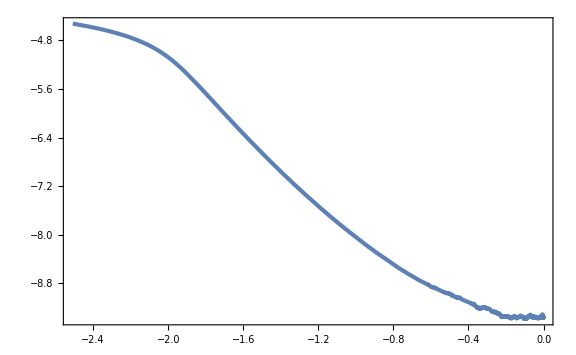

```mathematica
ParametricPlot[{(sample["PathFunction"][NN][[1]]-ϕc)/ϕc 10^5,Log10[Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]/M]},{NN,0,Nf}]
```

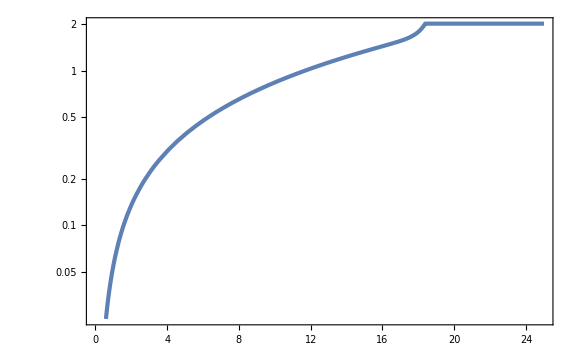

```mathematica
LogPlot[Abs[ηr[sample["PathFunction"][NN][[1]],Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]]],{NN,0,Nf}]//Quiet
```

```mathematica
deltaN=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Ninf[NN],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
Nf=25;
dNsampling=ParallelTable[RandomFunction[deltaN,{0,Nf,0.01}(*,10^3*)]["LastValues"],{i,10^4}]//Flatten;//AbsoluteTiming
```

{161.188,Null}

```mathematica
Export["N=15_1e4.csv",dNsampling];
```

```mathematica
dNsamplingN15=Import["N=15_1e4.csv"]//Flatten;
```

```mathematica
Mean[dNsamplingN15]
Variance[dNsamplingN15-Mean[dNsamplingN15]]
```

18.1567

0.0169463

```mathematica
Vx[x_]=Λ^4(1+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
Hx[x_,p_]=Sqrt[(p^2/2+Vx[x])/3];
ηrx[x_]=ηr[x,0];
```

```mathematica
Hxin=Hx[ϕc+15/μ1,0];
tf=50/Hxin;
hillsol=NDSolve[{x''[t]+3Hx[x[t],x'[t]]x'[t]+Vx'[x[t]]==0,NN'[t]==Hx[x[t],x'[t]],x[0]==ϕc+15/μ1,x'[0]==0,NN[0]==0,WhenEvent[ηrx[x[t]]==-2,Nend=NN[t];"StopIntegration"]},{x[t],NN[t]},{t,0,tf}][[1]];
```

```mathematica
Nend-Mean[dNsamplingN15]
```

2.96399

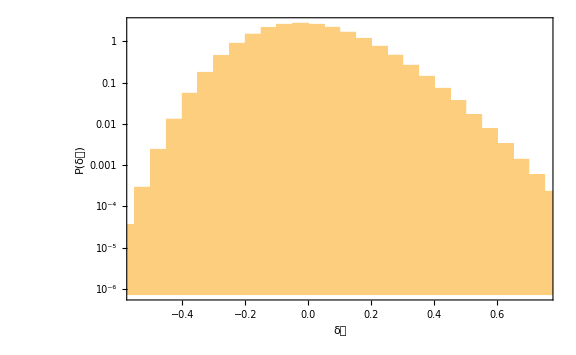

```mathematica
Histogram[dNsamplingN15-Mean[dNsamplingN15],Automatic,{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,n==15}}]
```

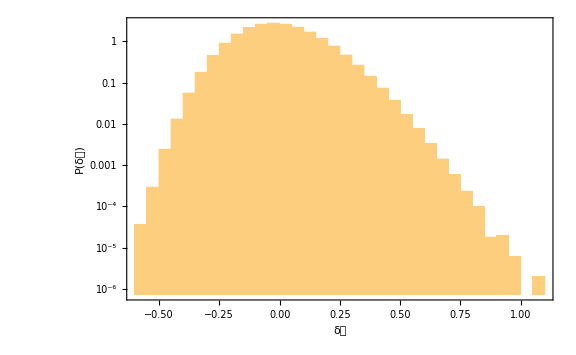

```mathematica
Histogram[dNsamplingN15-Mean[dNsamplingN15],30,{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,"waterfall = 15"}},PlotRange->Full]
```

```mathematica
dNpartN15=Partition[dNsamplingN15,10^6];
```

```mathematica
binListN15=HistogramList[dNsamplingN15-Mean[dNsamplingN15],30,"PDF"][[1]];
```

```mathematica
binListN15
```

{-3/5,-11/20,-1/2,-9/20,-2/5,-7/20,-3/10,-1/4,-1/5,-3/20,-1/10,-1/20,0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1,21/20,11/10}

```mathematica
HistoListN15=Table[HistogramList[dNpartN15[[i]]-Mean[dNpartN15[[i]]],{binListN15},"PDF"][[2]],{i,Length[dNpartN15]}]//Transpose;
```

```mathematica
JackHistoN15=Table[If[Mean[HistoListN15[[i]]]>0,{(binListN15[[i]]+binListN15[[i+1]])/2,Mean[HistoListN15[[i]]]±StandardDeviation[HistoListN15[[i]]]/Sqrt[10]},Nothing],{i,Length[binListN15]-1}];
JackHistoWOEN15=Table[If[Mean[HistoListN15[[i]]]>0,{(binListN15[[i]]+binListN15[[i+1]])/2,Mean[HistoListN15[[i]]]},Nothing],{i,Length[binListN15]-1}];
JackHistoErrN15=Table[If[Mean[HistoListN15[[i]]]>0,StandardDeviation[HistoListN15[[i]]]/Sqrt[10],Nothing],{i,Length[binListN15]-1}];
```

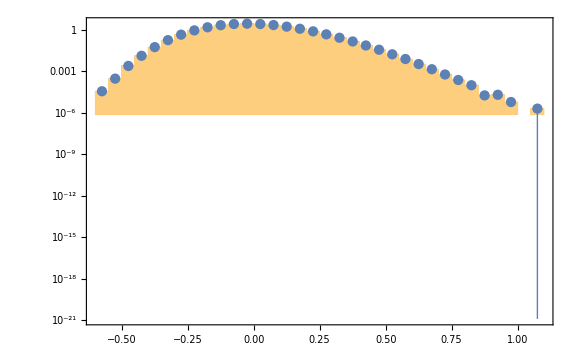

```mathematica
Show[Histogram[dNsamplingN15-Mean[dNsamplingN15],{binListN15},{"Log","PDF"},PlotRange->Full],ListLogPlot[JackHistoN15,Joined->False]]
```

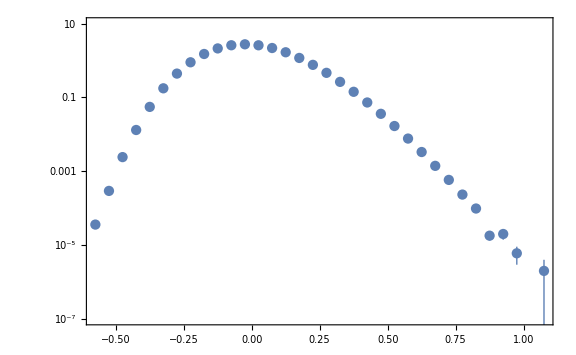

```mathematica
ListLogPlot[JackHistoN15,Joined->False,PlotRange->{10^-7,10}]
```

```mathematica
PDF[JohnsonDistribution["SU",γ,δ,μ,σ],x]
```

(ⅇ^(-1/2 (γ+δ ArcSinh[(x-μ)/σ])^2) δ)/(√(2 π) √((x-μ)^2+σ^2))

```mathematica
SUfitN15=NonlinearModelFit[JackHistoWOEN15,PDF[JohnsonDistribution["SU",γ,δ,μ,σ],x],{γ,δ,μ,σ},x(*,Weights->1/JackHistoErrN15^2*),MaxIterations->1000]
```

FittedModel[(3.00952 ⅇ^(-1/2 («1»)^2))/(√(0.406537+(«19»+x)^2))]

```mathematica
SUfitN15["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
γ | -8.59096 | 0.248751 | -34.5364 | 4.12412×10^-25
δ | 7.54374 | 0.0720628 | 104.683 | 6.01558×10^-39
μ | -0.904171 | 0.016719 | -54.0804 | 1.13107×10^-30
σ | 0.637602 | 0.00560449 | 113.766 | 5.41659×10^-40

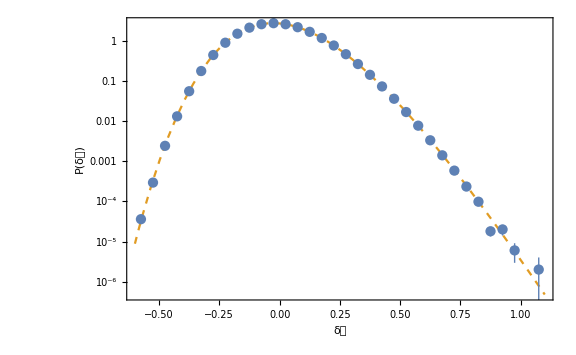

```mathematica
Show[LogPlot[Normal[SUfitN15],{x,-0.6,1.1},PlotStyle->{Color[2],Dashed},FrameLabel->{{P[δ𝒩],None},{δ𝒩,n==15}}],ListLogPlot[JackHistoN15,Joined->False]]
```

```mathematica
D[Log[Normal[SUfitN15]], x]/.{x->1}
```

-19.6108

## cubic

```mathematica
Π2=11^2;
μ1=Π2/(M^2 ϕc)
Λ=(As 12 π^2 μ1^-2)^(1/4)/.{As->2.1 10^-9}
ψr=Sqrt[(Λ^4 Sqrt[Π2])/(48Sqrt[2 π^3])]
μ2=6.6;
μ3=0.0415;
```

60500000 √2

2.41429×10^-6

9.94342×10^-13

```mathematica
Vx[x_]=Λ^4(1+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2+(x-ϕc)^3/μ3^3);
Hx[x_,p_]=Sqrt[(p^2/2+Vx[x])/3];
ηrx[x_]=ηr[x,0];
```

```mathematica
Hxin=Hx[ϕc,0];
tf=50/Hxin;
hillsol=NDSolve[{x''[t]+3Hx[x[t],x'[t]]x'[t]+Vx'[x[t]]==0,NN'[t]==Hx[x[t],x'[t]],x[0]==ϕc+30/μ1,x'[0]==0,NN[0]==0,WhenEvent[x[t]==ϕc,tc=t;"StopIntegration"]},{x[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];//Quiet
```

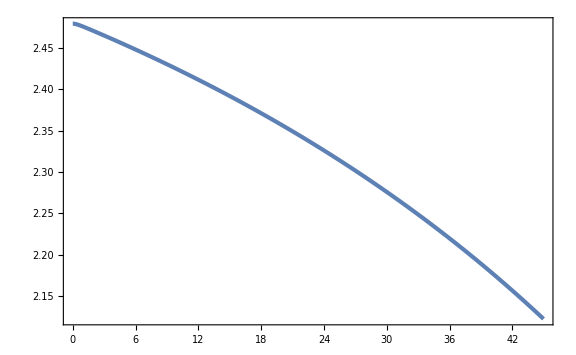

```mathematica
ParametricPlot[{NN[t]/.hillsol,(x[t]-ϕc)/ϕc 10^5/.hillsol},{t,0,tc}]
```

```mathematica
xsol[t_]=x[t]/.hillsol;
Nsol[t_]=NN[t]/.hillsol;
```

```mathematica
tCMB=t/.FindRoot[Nsol[tc]-Nsol[t]==30,{t,tc/10}];//Quiet
Nsol[tc]-Nsol[tCMB]
```

30.

```mathematica
1+2 Vx''[xsol[tCMB]]/Vx[xsol[tCMB]]
```

0.964967

### N = 2

```mathematica
ys={y1,y2};
pys={py1,py2};
wys={wy1,wy2};
ny=Length[ys];
ysN=Table[ys[[i]][NN],{i,ny}];
pysN=Table[pys[[i]][NN],{i,ny}];
```

```mathematica
V[x_,ys_]:=Λ^4((1-(ys.ys)/M^2)^2+2(x^2 ys.ys)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2+(x-ϕc)^3/μ3^3)
```

```mathematica
Vr[x_,yr_]=Λ^4((1-yr^2/M^2)^2+2(x^2 yr^2)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2+(x-ϕc)^3/μ3^3);
ηr[x_,yr_]=D[D[Vr[x,yr], yr], yr]/Vr[x,yr];
```

```mathematica
LogPlot[Abs[ηr[ϕc(1+dx 10^-5),0]],{dx,-4,2},GridLines->{None,{2}},FrameLabel->{Row[{"10^5 × ",(ϕ-Subscript[ϕ, "c"])/Subscript[ϕ, "c"]}],Abs[η]}]
```

-Graphics-

```mathematica
H[x_,ys_,px_,pys_]:=Sqrt[(px^2/2+(pys.pys)/2+V[x,ys])/3]
```

```mathematica
EoMx={ⅆx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](px[NN]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwx[NN]),
ⅆpx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3px[NN]-D[V[x[NN],ysN], x[NN]]/H[x[NN],ysN,px[NN],pysN])ⅆNN};
EoMy=Flatten[Table[{ⅆysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](pysN[[i]]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwys[[i]][NN]),
ⅆpysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3pysN[[i]]-D[V[x[NN],ysN], ysN[[i]]]/H[x[NN],ysN,px[NN],pysN])ⅆNN},{i,ny}]];
```

```mathematica
IV=Flatten[{ϕc,0,Table[ψr,{i,ny}],Table[0,{i,ny}],0}];
```

```mathematica
prob=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Flatten[{x[NN],px[NN],ysN,pysN,Ninf[NN]}],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
```

```mathematica
Nf=25;
sample=RandomFunction[prob,{0,Nf,0.01}];
```

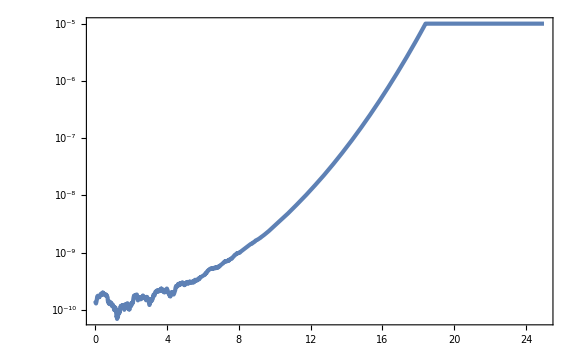

```mathematica
LogPlot[Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]/M,{NN,0,Nf}]
```

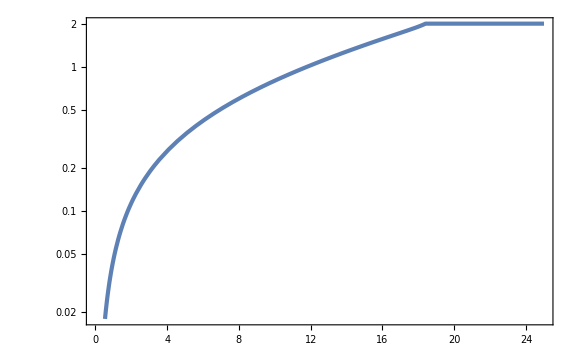

```mathematica
LogPlot[Abs[ηr[sample["PathFunction"][NN][[1]],Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]]],{NN,0,Nf}]//Quiet
```

```mathematica
deltaN=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Ninf[NN],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
Nf=25;
dNsampling=ParallelTable[RandomFunction[deltaN,{0,Nf,0.01},10^3]["LastValues"],10^4]//Flatten;//AbsoluteTiming
```

{14234.4,Null}

```mathematica
Export["N=2_cubic.csv",dNsampling];
```

```mathematica
dNsamplingN2=Import["N=2_cubic.csv"]//Flatten;
```

```mathematica
Mean[dNsamplingN2]
Variance[dNsamplingN2-Mean[dNsamplingN2]]
```

18.3642

0.0171388

```mathematica
Vx[x_]=Λ^4(1+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2+(x-ϕc)^3/μ3^3);
Hx[x_,p_]=Sqrt[(p^2/2+Vx[x])/3];
ηrx[x_]=ηr[x,0];
```

```mathematica
Hxin=Hx[ϕc,0];
tf=50/Hxin;
hillsol=NDSolve[{x''[t]+3Hx[x[t],x'[t]]x'[t]+Vx'[x[t]]==0,NN'[t]==Hx[x[t],x'[t]],x[0]==ϕc,x'[0]==0,NN[0]==0,WhenEvent[ηrx[x[t]]==-2,Nend=NN[t];"StopIntegration"]},{x[t],NN[t]},{t,0,tf}][[1]];
```

```mathematica
Nend-Mean[dNsamplingN2]
```

-0.185999

```mathematica
HistogramList[dNsamplingN2-Mean[dNsamplingN2],30]
```

{{-31/50,-3/5,-29/50,-14/25,-27/50,-13/25,-1/2,-12/25,-23/50,-11/25,-21/50,-2/5,-19/50,-9/25,-17/50,-8/25,-3/10,-7/25,-13/50,-6/25,-11/50,-1/5,-9/50,-4/25,-7/50,-3/25,-1/10,-2/25,-3/50,-1/25,-1/50,0,1/50,1/25,3/50,2/25,1/10,3/25,7/50,4/25,9/50,1/5,11/50,6/25},{1,0,4,13,37,93,242,518,1127,2148,3946,7154,12085,19800,30472,45180,65241,89470,119726,154408,194211,237389,280639,326418,370402,411209,448396,478814,504523,522230,532077,535053,532838,522636,506678,486665,465795,439768,411926,383792,354816,326035,176025}}

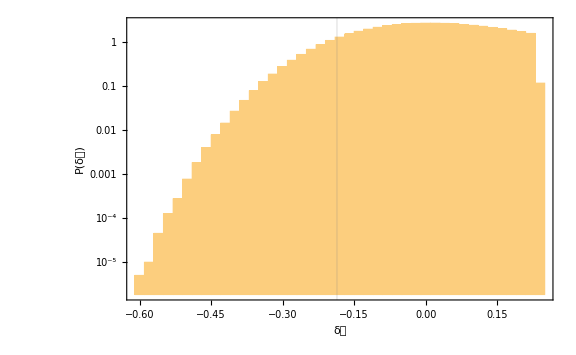

```mathematica
Histogram[dNsamplingN2-Mean[dNsamplingN2],{-0.61,0.25,0.02},{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,n==2}},PlotRange->Full,GridLines->{{Nend-Mean[dNsamplingN2]},None}]
```

```mathematica
dNpartN2=Partition[dNsamplingN2,10^6];
```

```mathematica
binListN2=HistogramList[dNsamplingN2-Mean[dNsamplingN2],{-0.61,0.25,0.02},"PDF"][[1]];
```

```mathematica
HistoListN2=Table[HistogramList[dNpartN2[[i]]-Mean[dNpartN2[[i]]],{binListN2},"PDF"][[2]],{i,Length[dNpartN2]}]//Transpose;
```

```mathematica
JackHistoN2=Table[{(binListN2[[i]]+binListN2[[i+1]])/2,Mean[HistoListN2[[i]]]±StandardDeviation[HistoListN2[[i]]]/Sqrt[10]},{i,Length[binListN2]-1}];
JackHistoWOEN2=Table[{(binListN2[[i]]+binListN2[[i+1]])/2,Mean[HistoListN2[[i]]]},{i,Length[binListN2]-1}];
JackHistoErrN2=Table[StandardDeviation[HistoListN2[[i]]]/Sqrt[10],{i,Length[binListN2]-1}];
```

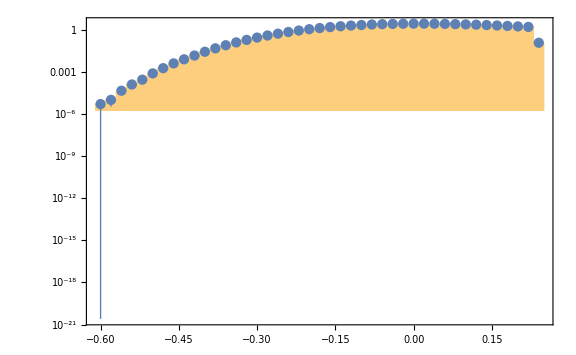

```mathematica
Show[Histogram[dNsamplingN2-Mean[dNsamplingN2],{binListN2},{"Log","PDF"},PlotRange->Full],ListLogPlot[JackHistoN2,Joined->False]]
```

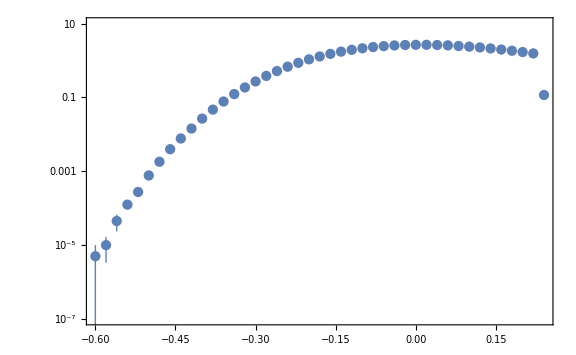

```mathematica
ListLogPlot[JackHistoN2,Joined->False,PlotRange->{10^-7,10}]
```

```mathematica
SUfitN2=NonlinearModelFit[Drop[JackHistoWOEN2,-1],PDF[JohnsonDistribution["SU",γ,δ,μ,σ],x],{γ,δ,μ,σ},x(*,Weights->1/Drop[JackHistoErrN2,-1]^2*),MaxIterations->100000]
```

FittedModel[(418.929 ⅇ^(-1/2 («1»)^2))/(√(800.935+(-154.192+x)^2))]

```mathematica
SUfitN2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
γ | 2516.72 | 1.61635×10^9 | 1.55704×10^-6 | 0.999999
δ | 1050.1 | 4.96151×10^7 | 0.0000211649 | 0.999983
μ | 154.192 | 1.45707×10^7 | 0.0000105823 | 0.999992
σ | 28.3008 | 3.83564×10^7 | 7.37838×10^-7 | 0.999999

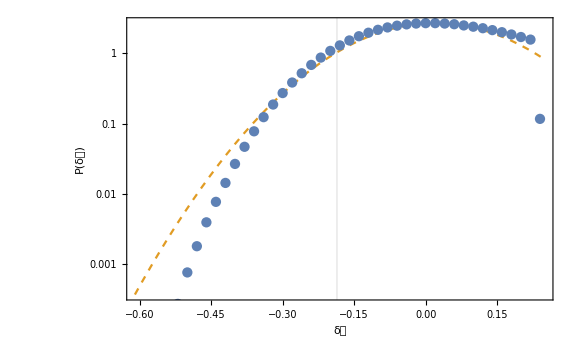

```mathematica
Show[LogPlot[Normal[SUfitN2],{x,-0.61,0.25},PlotStyle->{Color[2],Dashed},GridLines->{{Nend-Mean[dNsampling]},None},FrameLabel->{{P[δ𝒩],None},{δ𝒩,Row[{n==2,", cubic"}]}}],ListLogPlot[JackHistoN2,Joined->False]]
```